# When should genomic imprinting affect sexual maturation?

```mathematica
Clear["Global`*"]
```

## Parameters

```mathematica
tdip={tff->1/2,tmf->1/2,tfm->1/2,tmm->1/2};
thapdip={tff->1/2,tmf->1,tfm->1/2,tmm->0};
```

Fecundity and survival functions:

```mathematica
ϕ[a_]:=(k a)^3
σ[a_]:=Exp[-μ a]
```

## Fitness expressions a_f

w_ij: expected number of mutant offspring of sex i contributed by a sex j focal parent

```mathematica
wff=tff f[afi](((1-df)s[afjfi])/(f[afff](1-df)s[afjff]+f[af]df s[af])+(df s[afjfi])/(f[af]s[af]));
```

```mathematica
wmf=tmf f[afi]((nm(1-dm))/(nf(f[afff](1-dm)+f[af]dm))+(nm dm)/(nf f[af]));
wfm=tfm nf/nm(l f[affm](((1-df)s[afjmi])/(f[affm](1-df)s[afjfm]+f[af]df s[af])+(df s[afjmi])/(f[af]s[af]))+(1-l)s[afjminonloc]/s[af]);
wmm=tmm nf/nm(l f[affm]((nm(1-dm))/(nf(f[affm](1-dm)+f[af]dm))+(nm dm)/(nf f[af]))+(1-l)nm/nf);
```

## Fitness expressions a_m

```mathematica
wamff=tff ;
```

```mathematica
wammf=tmf ((nm(1-dm)s[amjfi])/(nf((1-dm)s[amjmf]+dm s[am]))+(nm dm s[amjfi])/(nf s[am]));
wamfm=tfm nf/nm(l f[ami]/f[ammm]+(1-l)f[ami]/f[am]);
wammm=tmm nf/nm(l f[ami]/f[ammm]((nm(1-dm)s[amjmi])/(nf((1-dm)s[amjmm]+dm s[am]))+(nm dm s[amjmi])/(nf s[am]))+(1-l)f[ami]/f[am](nm s[amjminonloc])/(nf s[am]));
```

## Reproductive values, class frequencies

Demographical model of homogeneous population

```mathematica
A={{wff,wfm},{wmf,wmm}}/.{affm->af,afff->af,afjfm->af,afjff->af,afjfi->af,afjmi->af,amjfi->am,amjmi->am,afi->af,afjminonloc->af,amjminonloc->am,amjmnonloc->am,afjmnonloc->af}//Simplify
```

{{tff,(nf tfm)/nm},{(nm tmf)/nf,tmm}}

```mathematica
evals=Simplify[Eigenvalues[A]]
```

{1/2 (tff+tmm-√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)),1/2 (tff+tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2))}

```mathematica
classfreqs=Simplify[Eigenvectors[1/evals[[1]] A]]
```

{{(nf (tff-tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nm tmf),1},{-(nf (-tff+tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nm tmf),1}}

```mathematica
repvals=Simplify[Eigenvectors[1/evals[[1]] Transpose[A]]]
```

{{(nm (tff-tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nf tfm),1},{-(nm (-tff+tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nf tfm),1}}

### Diplodiploidy

Stable class frequencies

```mathematica
udipR=Simplify[classfreqs[[1]]/Total[classfreqs[[1]]]/.tdip]
```

{nf/(nf+nm),nm/(nf+nm)}

```mathematica
udip={uf->udipR[[1]],um->udipR[[2]]};
```

Individual reproductive values

```mathematica
vdipR=Simplify[repvals[[1]]/(udipR.repvals[[1]])/.tdip]
```

{(nf+nm)/(2 nf),(nf+nm)/(2 nm)}

```mathematica
vdip={vf->vdipR[[1]],vm->vdipR[[2]]};
```

Class reproductive values

```mathematica
cdip={cf->vf uf,cm->vm um}/.vdip/.udip
```

{cf→1/2,cm→1/2}

### Haplodiploidy

```mathematica
uhapdipR=Simplify[classfreqs[[1]]/Total[classfreqs[[1]]]/.thapdip]
```

{nf/(nf+nm),nm/(nf+nm)}

```mathematica
uhapdip={uf->uhapdipR[[1]],um->uhapdipR[[2]]};
```

Individual reproductive values

```mathematica
vhapdipR=Simplify[repvals[[1]]/(uhapdipR.repvals[[1]])/.thapdip]
```

{(2 (nf+nm))/(3 nf),(nf+nm)/(3 nm)}

```mathematica
vhapdip={vf->vhapdipR[[1]],vm->vhapdipR[[2]]};
```

Class reproductive values

```mathematica
chapdip={cf->vf uf,cm->vm um}/.vhapdip/.uhapdip
```

{cf→2/3,cm→1/3}

## Selection gradient on a_f

```mathematica
Wfaf=wff+vm/vf wmf;
Wmaf=wmm+vf/vm wfm;
```

```mathematica
selgradaf=cf(
D[Wfaf,afi]rfi
+D[Wfaf,afjfi]rfownjf
+D[Wfaf,afff]rff
+D[Wfaf,afjff]rflocjf
)+cm(
D[Wmaf,afjmi]rmownjf+
D[Wmaf,afjminonloc]rmownjfnonloc+
D[Wmaf,affm]rmf+
D[Wmaf,afjfm]rmlocjf
)/.{afi->af,afjfi->af,afjmi->af,afjminonloc->af,afff->af,afjff->af,affm->af,afjfm->af,afjmnonloc->af}//Simplify
```

-((cf nm vm (nf ((-1+df)^2 rff-rfi) tff vf+nm ((-1+dm)^2 rff-rfi) tmf vm)+cm l nf rmf vf (-2 df nf tfm vf+df^2 nf tfm vf+(-2+dm) dm nm tmm vm)) s[af] f'[af]+nf vf (cm nf (-rmownjfnonloc+l ((-1+df)^2 rmlocjf-rmownjf+rmownjfnonloc)) tfm vf+cf nm ((-1+df)^2 rflocjf-rfownjf) tff vm) f[af] s'[af])/(nf nm vf vm f[af] s[af])

## Selection gradient on a_m

```mathematica
Wfam=wamff+vm/vf wammf;
Wmam=wammm+vf/vm wamfm;
```

```mathematica
Wmam//Variables
```

{nf,nm,tfm,vf,vm,l,f[am],f[ami],f[ammm],tmm,s[am],s[amjminonloc],dm,s[amjmi],s[amjmm]}

```mathematica
selgradam=cf(
D[Wfam,amjfi]rfownjm
+D[Wfam,amjmf]rflocjm
)+cm(
D[Wmam,ami]rmi
+D[Wmam,amjmi]rmownjm
+D[Wmam,amjminonloc]rmownjmnonloc
+D[Wmam,ammm]rmm
+D[Wmam,amjmm]rmlocjm
+D[Wmam,amjmnonloc]rmnonlocjm
)/.{amjmi->am,amjfi->am,amjmf->am,ami->am,ammm->am,amjmm->am,amjminonloc->am,amjmnonloc->am}//Simplify
```

(cm (rmi-l rmm) (nf tfm vf+nm tmm vm) f'[am])/(nm vm f[am])-((cm nf (-rmownjmnonloc+l ((-1+dm)^2 rmlocjm-rmownjm+rmownjmnonloc)) tmm vf+cf nm ((-1+dm)^2 rflocjm-rfownjm) tmf vm) s'[am])/(nf vf s[am])

## Relatedness

### Diplodiploidy

#### Coefficients of consanguinity

```mathematica
hf=1-df;
hm=1-dm;
```

```mathematica
Qdip={QffJ==QmmJ==QfmJ==1/4(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm+1/4 l^2(1/nm Qm+(nm-1)/nm Qmm),
Qf==1/2(1+l Qfm),
Qf==Qm,
Qff==hf^2 QffJ,
Qmm==hm^2 QmmJ,
Qfm==hf hm QfmJ,
Qmf==Qfm};
```

```mathematica
Qsoldip=Solve[Qdip,{QffJ,QmmJ,QfmJ,Qff,Qf,Qm,Qmm,Qfm,Qmf}]//Simplify//Flatten;
```

#### Relatedness coefficients

```mathematica
rdip={
rfi->Qf,
rmi->Qm,
rfownjm->Qf,
rfownjf->Qm,
rmownjf->1/2+1/2 Qfm,
rmownjm->1/2+1/2 Qfm,
rmownjfnonloc->1/2,
rmownjmnonloc->1/2,
rff->1/nf Qf+(nf-1)/nf Qff,
rmf->Qmf,
rmm->l 1/nm Qm+l(nm-1)/nm Qmm,
rflocjf->1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm),
rflocjm->1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm),
rmlocjf->1/2 1/nm l(Qm+Qfm)+1/2 l(nm-1)/nm(Qfm+Qmm)+1/2(1-l)Qfm,
rmlocjm->1/2 1/nm l(Qm+Qfm)+1/2 l(nm-1)/nm(Qfm+ Qmm)+1/2(1-l)Qfm
}/.Qsoldip;
```

```mathematica
rdipM={
rfi->1/2(Qf+l Qfm),
rmi->1/2(Qf+l Qfm),
rfownjm->Qf,
rfownjf->Qf,
rmownjf->Qfm,
rmownjm->Qfm,
rmownjfnonloc->0,
rmownjmnonloc->0,
rff->1/2 1/nf(Qf+l Qfm)+(nf-1)/nf hf^2(1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm)),
rmf->1/2 hm hf(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rmm->1/2 1/nm l(Qf+l Qfm)+ hm^2(nm-1)/nm l(1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm)),
rflocjf->1/nf Qf+(nf-1)/nf Qff,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->Qfm,
rmlocjm->Qfm
}/.Qsoldip;
```

Expression by father (P)

```mathematica
rdipP={
rfi->1/2(Qm+l Qfm),
rmi-> 1/2(Qm+l Qfm),
rfownjf->l Qfm,
rfownjm->l Qfm,
rmownjm->Qm,
rmownjf->Qm,
rmownjfnonloc->Qm,
rmownjmnonloc->Qm,
rff->1/2 1/nf(Qm+l Qfm)+1/2(nf-1)/nf hf^2(1/nm l(Qm+Qfm)+(nm-1)/nm l(l Qmm+Qfm)),
rmf->1/2 hf hm (1/nm l(Qm+Qfm)+(nm-1)/nm l(l Qmm+Qfm)),
rmm->1/2 1/nm l(Qm+l Qfm)+1/2(nm-1)/nm hm^2 l(1/nm l(Qm+Qfm)+(nm-1)/nm l(l Qmm+Qfm)),
rflocjf->l Qfm,
rflocjm->l Qfm,
rmlocjf->l 1/nm Qm+l (nm-1)/nm Qmm,
rmlocjm->l 1/nm Qm+l (nm-1)/nm Qmm
}/.Qsoldip;
```

Expression by maternally-inherited alleles (MI)

```mathematica
rdipMI={
rfi->Qf,
rmi->Qm,
rfownjf->1,
rfownjm->1,
rmownjf->Qfm,
rmownjm->Qfm,
rmownjfnonloc->0,
rmownjmnonloc->0,
rff->1/nf Qf+1/2(nf-1)/nf hf^2(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rfm->1/2 hm hf 1/nf(Qf+l Qfm)+1/2 hm hf(nf-1)/nf(Qff+l Qfm),
rmf->1/2 hm hf 1/nf(Qf+l Qfm)+1/2 hm hf(nf-1)/nf(Qff+l Qfm),
rmm->l 1/nm Qf+1/2(nm-1)/nm hm^2 l(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rflocjf->1/nf Qf+(nf-1)/nf Qff,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->Qmf,
rmlocjm->Qmf}/.Qsoldip;
```

```mathematica
rdipPI={
rfi->Qf,
rmi->Qm,
rfownjf->l Qfm,
rfownjm->l Qfm,
rmownjf->1,
rmownjm->1,
rmownjfnonloc->1,
rmownjmnonloc->1,
rff->1/nf Qm+1/2(nf-1)/nf hf^2(1/nm l(Qm+Qfm)+(nm-1)/nm l(l Qmm+Qfm)),
rfm->1/2 hf hm (l 1/nm(Qm+Qfm)+(nm-1)/nm l (l Qmm+Qfm)),
rmf->1/2 hf hm (l 1/nm(Qm+Qfm)+(nm-1)/nm l (l Qmm+Qfm)),
rmm->l 1/nm Qm+1/2(nm-1)/nm hm^2 l(1/nm l(Qm+Qfm)+(nm-1)/nm l(l Qmm+Qfm)),
rflocjf->l Qfm,
rflocjm->l Qfm,
rmlocjf->l(1/nm Qm+(nm-1)/nm Qmm),
rmlocjm->l(1/nm Qm+(nm-1)/nm Qmm)}/.Qsoldip;
```

### Haplodiploidy

#### Coefficients of consanguinity haplodiploidy

```mathematica
Qhapdip={QffJ==1/4(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm+1/4 l^2(1/nm Qm+(nm-1)/nm Qmm),
QfmJ==QmfJ==1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
QmmJ==1/nf Qf+(nf-1)/nf Qff,
Qf==1/2(1+l Qfm),
Qm==1,
Qff==hf^2 QffJ,
Qmm==hm^2 QmmJ,
Qfm==hf hm QfmJ,
Qmf==Qfm};
```

```mathematica
Qsolhapdip=Solve[Qhapdip,{QffJ,QmmJ,QfmJ,QmfJ,Qff,Qf,Qm,Qmm,Qfm,Qmf}]//Simplify//Flatten;
```

#### Relatedness coefficients haplodiploidy

Expression of alleles in offspring

```mathematica
rhapdip={
rfi->Qf,
rmi->Qm,
rfownjf->Qf,
rfownjm->Qm,
rmownjf->1/2 Qm+1/2 Qfm,
rmownjm->Qfm,
rmownjfnonloc->1/2,
rmownjmnonloc->0,
rff->1/nf Qf+(nf-1)/nf Qff,
rfm->Qmf,
rmf->Qmf,
rmm->l 1/nm Qm+l(nm-1)/nm Qmm,
rflocjf->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->1/2 1/nm l(Qm+Qfm)+1/2 l (nm-1)/nm(Qfm+Qmm)+1/2(1-l)Qfm,
rmlocjm->Qmf
}/.Qsolhapdip;
```

Expression controlled by mother (M)

```mathematica
rhapdipM={
rfi->1/2(Qf+l Qfm),
rmi->Qf,
rfownjf->Qf,
rfownjm->Qf,
rmownjf->Qfm,
rmownjm->Qfm,
rmownjfnonloc->0,
rmownjmnonloc->0,
rff->1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf hf^2(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rfm->1/2 hf hm(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rmf->hf hm(1/nf Qf+(nf-1)/nf Qff),
rmm->l 1/nm Qf+(nm-1)/nm hm^2 l(1/nf Qf+(nf-1)/nf Qff),
rflocjf->1/nf Qf+(nf-1)/nf Qff,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->Qmf,
rmlocjm->Qmf
}/.Qsolhapdip;
```

Expression controlled by father (P)

```mathematica
rhapdipP={
rfi->1/2(Qm+l Qfm),
rmi->Qm,
rfownjf->l Qfm,
rfownjm->Qm,
rmownjf->Qm,
rmownjm->Qfm,
rmownjfnonloc->Qm,
rmownjmnonloc->0,
rff->1/2 1/nf(Qm+l Qfm)+1/2(nf-1)/nf hf^2(1/nm l(Qm+Qfm)+(nm-1)/nm l (l Qmm+Qfm)),
rfm->Qmf,
rmf->hm hf Qmf,
rmm->l 1/nm Qm+l(nm-1)/nm Qmm,
rflocjf->l Qfm,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->l(1/nm Qm+(nm-1)/nm Qmm),
rmlocjm->Qmf
}/.Qsolhapdip;
```

```mathematica
rhapdipMI={
rfi->Qf,
rmi->Qm,
rfownjf->1,
rfownjm->1,
rmownjf->Qfm,
rmownjm->Qfm,
rmownjfnonloc->0,
rmownjmnonloc->0,
rff->1/nf Qf+1/2(nf-1)/nf hf^2(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rfm->1/2 hf hm(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rmf->hf hm(1/nf Qf+(nf-1)/nf Qff),
rmm->l 1/nm Qm+(nm-1)/nm hm^2 l(1/nf Qf+(nf-1)/nf Qff),
rflocjf->1/nf Qf+(nf-1)/nf Qff,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->Qmf,
rmlocjm->Qmf}/.Qsolhapdip;
```

```mathematica
rhapdipPI={
rfi->Qf,
rmi->Qm,
rfownjf->l Qfm,
rfownjm->Qm,
rmownjf->1,
rmownjm->Qfm,
rmownjfnonloc->Qm,
rmownjmnonloc->0,
rff->1/nf Qf+(nf-1)/nf hf^2(l 1/nm Qf+(nm-1)/nm l(l Qmm+Qmf)),
rmf->l Qmf,
rfm->Qmf,
rmm->l 1/nm Qm+l(nm-1)/nm Qmm,
rflocjf->l Qfm,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->l(1/nm Qm+(nm-1)/nm Qmm),
rmlocjm->Qmf}/.Qsolhapdip;
```

## Analytical results diplodiploidy

```mathematica
afamsol=Solve[{selgradaf==0,selgradam==0},{s'[af],s'[am]}]/.vdip/.cdip/.{tff->1/2,tfm->1/2,tmf->1/2,tmm->1/2}//FullSimplify//Flatten
```

{s'[af]→-(((2+(-2+df) df+(-2+dm) dm) rff-2 rfi+((-2+df) df+(-2+dm) dm) l rmf) s[af] f'[af])/(((-1+df)^2 rflocjf-rfownjf+(-1+df)^2 l rmlocjf-l rmownjf+(-1+l) rmownjfnonloc) f[af]),s'[am]→(2 (rmi-l rmm) s[am] f'[am])/(((-1+dm)^2 rflocjm-rfownjm+(-1+dm)^2 l rmlocjm-l rmownjm+(-1+l) rmownjmnonloc) f[am])}

```mathematica
rfcoeff={rfselfjuvf->rfkidf+l rmkidf+(1-l)rmkidfnonloc,
rfcompetingjuvf->hf^2(rflocjf+l rmlocjf),
rfownoffspring->rfi+l rmf,
rfcompetingoffspring->1/2(hf^2+hm^2)(rff+l rmf)
};
rmcoeff={rmselfjuvm->l rmkidm+rfkidm+(1-l)rmkidmnonloc,
rmcompetingjuvm->hm^2(rflocjm+l rmlocjm),
rmownoffspring->rmi,
rmcompetingoffspring->l rmm};
```

```mathematica
s'[af]/.afamsol
```

-(((2+(-2+df) df+(-2+dm) dm) rff-2 rfi+((-2+df) df+(-2+dm) dm) l rmf) s[af] f'[af])/(((-1+df)^2 rflocjf-rfownjf+(-1+df)^2 l rmlocjf-l rmownjf+(-1+l) rmownjfnonloc) f[af])

Check algebra s’[af]

```mathematica
(((rfownoffspring-rfcompetingoffspring)s[af])/(-1/2(rfselfjuvf-rfcompetingjuvf))f'[af]/f[af]/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc})==(s'[af]/.afamsol)//Simplify
```

True

```mathematica
s'[af]/.afamsol//Simplify
```

-(((2+(-2+df) df+(-2+dm) dm) rff-2 rfi+((-2+df) df+(-2+dm) dm) l rmf) s[af] f'[af])/(((-1+df)^2 rflocjf-rfownjf+(-1+df)^2 l rmlocjf-l rmownjf+(-1+l) rmownjfnonloc) f[af])

```mathematica
(((rfownoffspring-rfcompetingoffspring)s[af])/(-1/2(rfselfjuvf-rfcompetingjuvf))f'[af]/f[af]/.rfcoeff)==(s'[af]/.afamsol)//FullSimplify
```

(((2+(-2+df) df+(-2+dm) dm) rff-2 rfi+((-2+df) df+(-2+dm) dm) l rmf) (rfkidf-rfownjf+rmkidfnonloc-rmownjfnonloc+l (rmkidf-rmkidfnonloc-rmownjf+rmownjfnonloc)) s[af] f'[af])/((rfkidf-(-1+df)^2 rflocjf+rmkidfnonloc+l (rmkidf-rmkidfnonloc-(-1+df)^2 rmlocjf)) ((-1+df)^2 rflocjf-rfownjf+(-1+df)^2 l rmlocjf-l rmownjf+(-1+l) rmownjfnonloc) f[af])==0

Check algebra s’[am]

```mathematica
(((rmownoffspring-rmcompetingoffspring)s[am])/(-1/2(rmselfjuvm-rmcompetingjuvm))f'[am]/f[am]/.rmcoeff)==(s'[am]/.afamsol)//Simplify
```

(2 (rmi-l rmm) (1/(-rfkidm-l rmkidm+(-1+l) rmkidmnonloc+(-1+dm)^2 (rflocjm+l rmlocjm))-1/((-1+dm)^2 rflocjm-rfownjm+(-1+dm)^2 l rmlocjm-l rmownjm+(-1+l) rmownjmnonloc)) s[am] f'[am])/f[am]==0

```mathematica
{.5(rfselfjuvf)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdip/.{l->1,nm->2,nf->2,dm->1-df}}
```

{0.5 (1/2+(2 (-1+df) df)/(-20 (-1+df) df+4 df^2+4 (-7-2 df+df^2))+(-8 (-1+df) df+2 df^2+2 (-7-2 df+df^2))/(-20 (-1+df) df+4 df^2+4 (-7-2 df+df^2)))}

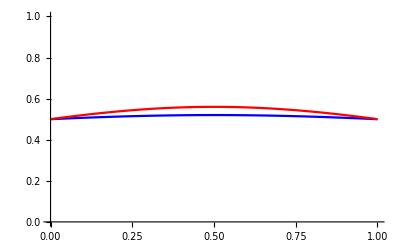

```mathematica
Plot[{{.5(rfselfjuvf)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdip/.{l->1,nm->2,nf->2,dm->1-df}},
{(rfownoffspring)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdip/.{l->1,nm->2,nf->2,dm->1-df}}},
{df,0,1},PlotStyle->{Blue,Red},PlotRange->{{0,1},{0,1}}]
```

```mathematica
(rfownoffspring-1/2 rfselfjuvf)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdip/.{nf->n,l->1,nm->n}/.{dm->1-𝒽m,df->1-𝒽f}//FullSimplify
```

-(𝒽f 𝒽m)/(-𝒽f^2+(𝒽f-𝒽m) 𝒽m+n (-2+𝒽f+𝒽m) (2+𝒽f+𝒽m))

### Left and right hand side relatedness of female trade-off function: r_(f,selfjuvf)-r_(f,competingjuvf)

```mathematica
relplot[relatedness_,plotLabel_,legend_:False,ticks_:{None,None}]:=Module[{legendType,labelstyle,thickval},
If[legend,legendType=Placed[{"r_(f→self,juv f)","r_(f→competing juv f)","r_(f→own offspring)","r_(f→competing offspring)","r_(f→self,juv f) - r_(f→competing juv f)","r_(f→own offspring) - r_(f→competing offspring)"},Right],legendType=None];
labelstyle={{Directive[FontOpacity->0,FontSize->0]},{Directive[FontOpacity->0,FontSize->0]}};
If[Count[{ticks[[1]]},None]==0,labelstyle[[1]]=Black];
If[Count[{ticks[[2]]},None]==0,labelstyle[[2]]=Black];
thickval=0.0075;
Plot[{.5(rfselfjuvf)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.relatedness/.{l->1,nm->2,nf->2,dm->1-df},
.5(rfcompetingjuvf)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.relatedness/.{l->1,nm->2,nf->2,dm->1-df},
{(rfownoffspring)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.relatedness/.{l->1,nm->2,nf->2,dm->1-df}},
{(rfcompetingoffspring)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.relatedness/.{l->1,nm->2,nf->2,dm->1-df}},
{0.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.relatedness/.{l->1,nm->2,nf->2,dm->1-df}},
{(rfownoffspring-rfcompetingoffspring)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.relatedness/.{l->1,nm->2,nf->2,dm->1-df}}
}
,
{df,0,1},
PlotLabel->plotLabel,
LabelStyle->{FontFamily->"Helvetica",Black},
(* ImagePadding->{{Scaled[0.05],Scaled[0.05]},{Scaled[0.01],Scaled[0.01]}},*)
PlotStyle->{
{Thickness[thickval],Red,Dashing[{0.001,0.01}]},
{Thickness[thickval],Red,Dashed},
{Thickness[thickval],Blue,Dashing[{0.001,0.01}]},
{Thickness[thickval],Blue,Dashed},
{Thickness[thickval*2],Red},
{Thickness[thickval*2],Blue}},PlotLegends->legendType,
TicksStyle->labelstyle,
PlotRange->{{0,1},{0,0.65}}]
]
```

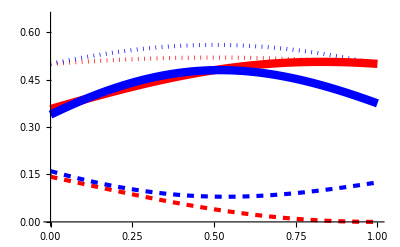

```mathematica
relplot[rdip,None,False,{None,Automatic}]
```

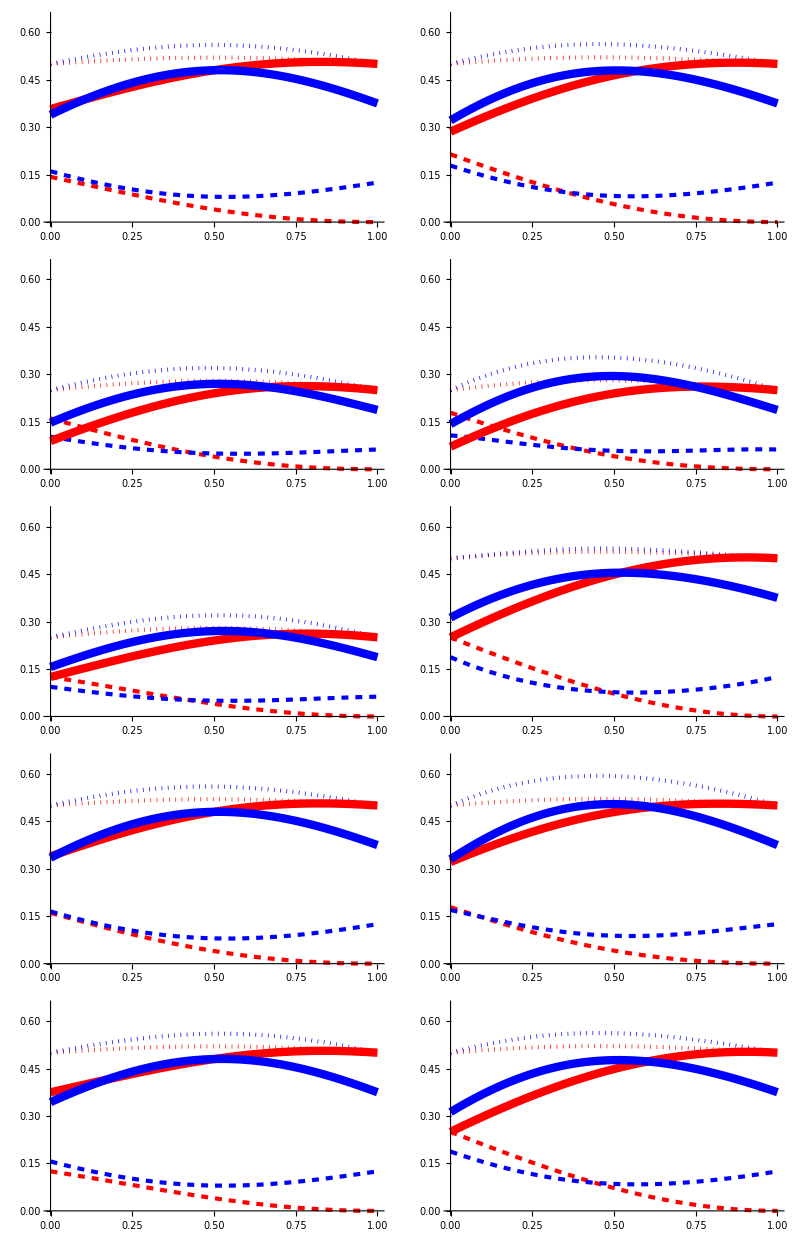
-Graphics-Sex-biased dispersal, d_f=1-d_mRelatedness r

```mathematica
theplot=Labeled[GraphicsGrid[
Transpose[{{
relplot[rdip,None,False,{None,Automatic}],
relplot[rdipM,None,False,{None,Automatic}],
relplot[rdipP,None,False,{None,Automatic}],
relplot[rdipMI,None,False,{None,Automatic}],
relplot[rdipPI,None,False,{Automatic,Automatic}]},
{relplot[rhapdip,None,False,{None,None}],
relplot[rhapdipM,None,False,{None,None}],
relplot[rhapdipP,None,False,{None,None}],
relplot[rhapdipMI,None,False,{None,None}],
relplot[rhapdipPI,None,False,{Automatic,None}]}
}],
Spacings->{0,0}
],{"Sex-biased dispersal, d_f=1-d_m","Relatedness r"},{Bottom,Left},
RotateLabel->True,
LabelStyle->{FontFamily->"Helvetica"}]
```

```mathematica
Export[$HomeDirectory<>"/Projects/age_vs_size_imprint/figs/effect_phil/relatedness.svg",theplot,ImageSize->{300,600}]
```

/home/bram/Projects/age_vs_size_imprint/figs/effect_phil/relatedness.svg

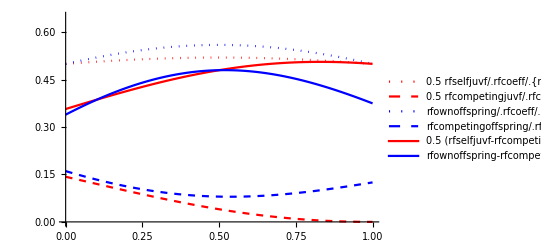

```mathematica
Plot[{.5(rfselfjuvf)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdip/.{l->1,nm->2,nf->2,dm->1-df},
.5(rfcompetingjuvf)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdip/.{l->1,nm->2,nf->2,dm->1-df},
{(rfownoffspring)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdip/.{l->1,nm->2,nf->2,dm->1-df}},
{(rfcompetingoffspring)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdip/.{l->1,nm->2,nf->2,dm->1-df}},
{0.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdip/.{l->1,nm->2,nf->2,dm->1-df}},
{(rfownoffspring-rfcompetingoffspring)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdip/.{l->1,nm->2,nf->2,dm->1-df}}
}
,
{df,0,1},PlotStyle->{{Red,Dotted},{Red,Dashed},{Blue,Dotted},{Blue,Dashed},{Red},{Blue}},PlotLegends->"Expressions",PlotRange->{{0,1},{0,0.65}}]
```

### Left and right hand side relatedness of female trade-off function: r_(f,selfjuvf)-r_(f,competingjuvf) for maternal imprint

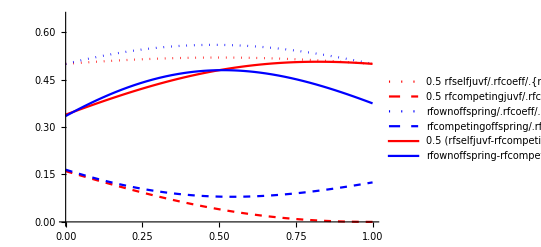

```mathematica
Plot[{.5(rfselfjuvf)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdipMI/.{l->1,nm->2,nf->2,dm->1-df},
.5(rfcompetingjuvf)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdipMI/.{l->1,nm->2,nf->2,dm->1-df},
{(rfownoffspring)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdipMI/.{l->1,nm->2,nf->2,dm->1-df}},
{(rfcompetingoffspring)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdipMI/.{l->1,nm->2,nf->2,dm->1-df}},
{0.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdipMI/.{l->1,nm->2,nf->2,dm->1-df}},
{(rfownoffspring-rfcompetingoffspring)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdipMI/.{l->1,nm->2,nf->2,dm->1-df}}
}
,
{df,0,1},PlotStyle->{{Red,Dotted},{Red,Dashed},{Blue,Dotted},{Blue,Dashed},{Red},{Blue}},PlotLegends->"Expressions",PlotRange->{{0,1},{0,0.65}}]
```

### Left and right hand side relatedness of female trade-off function: r_(f,selfjuvf)-r_(f,competingjuvf) for maternal effect

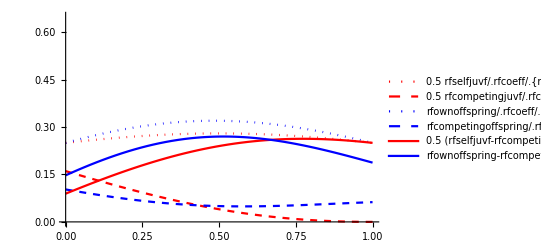

```mathematica
Plot[{.5(rfselfjuvf)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdipM/.{l->1,nm->2,nf->2,dm->1-df},
.5(rfcompetingjuvf)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdipM/.{l->1,nm->2,nf->2,dm->1-df},
{(rfownoffspring)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdipM/.{l->1,nm->2,nf->2,dm->1-df}},
{(rfcompetingoffspring)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdipM/.{l->1,nm->2,nf->2,dm->1-df}},
{0.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdipM/.{l->1,nm->2,nf->2,dm->1-df}},
{(rfownoffspring-rfcompetingoffspring)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdipM/.{l->1,nm->2,nf->2,dm->1-df}}
}
,
{df,0,1},PlotStyle->{{Red,Dotted},{Red,Dashed},{Blue,Dotted},{Blue,Dashed},{Red},{Blue}},PlotLegends->"Expressions",PlotRange->{{0,1},{0,0.65}}]
```

### Right hand side of female trade-off function: r_(f,own young)-r_(f,competing young)

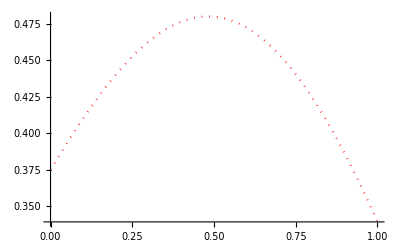

```mathematica
Plot[{(rfownoffspring-rfcompetingoffspring)/.rfcoeff/.{rfkidf->rfownjf,rmkidf->rmownjf,rmkidfnonloc->rmownjfnonloc}/.rdip/.{l->1,nm->2,nf->2,df->1-dm}},
{dm,0,1},PlotStyle->{{Red,Dotted},{Red,Dashed},{Red},{Blue,Dotted},{Blue,Dashed},{Blue}}]
```

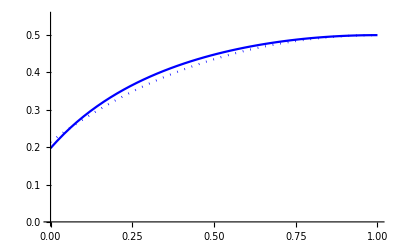

```mathematica
Plot[{.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm}
},
{dm,0,1},PlotStyle->{{Red},{Red,Dotted},{Blue},{Blue,Dotted}},PlotRange->{{0,1},{0,.55}}]
```

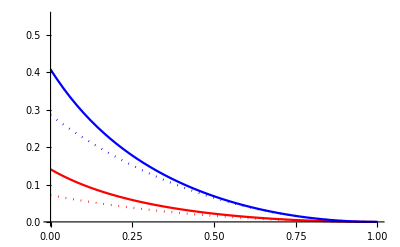

```mathematica
Plot[{.5rfcompetingjuvf/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
.5 rfcompetingjuvf/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm},
rfcompetingoffspring/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
rfcompetingoffspring/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm}
},
{dm,0,1},PlotStyle->{{Red},{Red,Dotted},{Blue},{Blue,Dotted}},PlotRange->{{0,1},{0,.55}}]
```

## Results diplodiploidy

```mathematica
ans[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf+selgradam==0,selgradam+selgradaf==0}/.rdip/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ansMI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf+selgradam,selgradam+selgradaf}/.rdipMI/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ansPI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf+selgradam,selgradam+selgradaf}/.rdipPI/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ansM[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf+selgradam,selgradam+selgradaf}/.rdipM/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ansP[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf+selgradam,selgradam+selgradaf}/.rdipP/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ans[{2,2},{0.5,0.9,1},{1,1/3}]
```

{af→2.37772,am→2.01562}

### Figure 1

```mathematica
kk=1/3
```

1/3

```mathematica
μx=1
```

1

```mathematica
ll=1.0
```

1.

```mathematica
a1=Table[{{dm,af},{dm,am}}/.ans[{2,2},{1-dm,dm,ll},{μx,kk}],{dm,0.01,1,0.01}];
a2=Table[{{dm,af},{dm,am}}/.ansM[{2,2},{1-dm,dm,ll},{μx,kk}],{dm,0.01,1,0.01}];
a3=Table[{{dm,af},{dm,am}}/.ansP[{2,2},{1-dm,dm,ll},{μx,kk}],{dm,0.01,1,0.01}];
a4=Table[{{dm,af},{dm,am}}/.ansMI[{2,2},{1-dm,dm,ll},{μx,kk}],{dm,0.01,1,0.01}];
a5=Table[{{dm,af},{dm,am}}/.ansPI[{2,2},{1-dm,dm,ll},{μx,kk}],{dm,0.01,1,0.01}];
```

```mathematica
Export["data.mx",a1]
```

data.mx

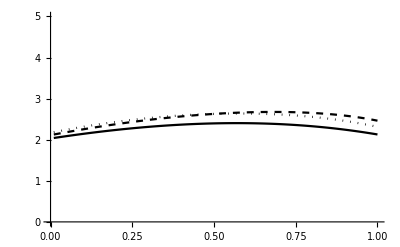

```mathematica
plotbattle1=ListLinePlot[{Transpose[a1][[1]],Transpose[a2][[1]],Transpose[a3][[1]]},PlotStyle->{{Black,Normal},{Black,Dashed},{Black,Dotted}},PlotRange->{{0,1},{0,5}},BaseStyle->{FontFamily->"Helvetica"}]
```

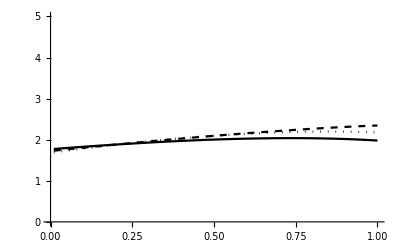

```mathematica
plotbattle1m=ListLinePlot[{Transpose[a1][[2]],Transpose[a2][[2]],Transpose[a3][[2]]},PlotStyle->{{Black,Normal},{Black,Dashed},{Black,Dotted}},PlotRange->{{0,1},{0,5}},BaseStyle->{FontFamily->"Helvetica"}]
```

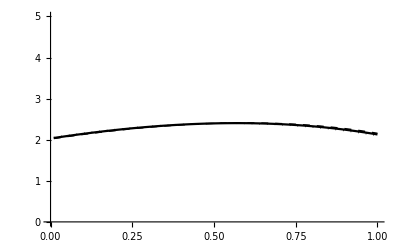

```mathematica
plotbattle2=ListLinePlot[{Transpose[a1][[1]],Transpose[a4][[1]],Transpose[a5][[1]]},PlotStyle->{{Black,Normal},{Black,Dashed,Thick},{Black,Dotted,Thick}},PlotRange->{{0,1},{0,5}},BaseStyle->{FontFamily->"Helvetica"}]
```

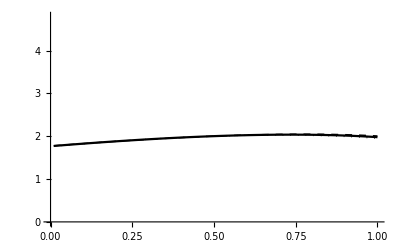

```mathematica
plotbattle2m=ListLinePlot[{Transpose[a1][[2]],Transpose[a4][[2]],Transpose[a5][[2]]},PlotStyle->{{Black,Normal},{Black,Dashed,Thick},{Black,Dotted,Thick}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

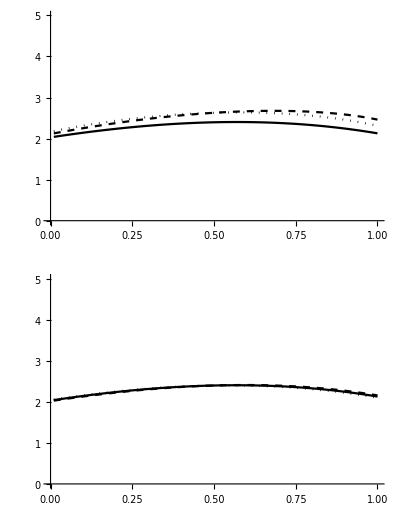
-Graphics-Sex-biased dispersal, d_m=1-d_fFemale age at maturity, a_f

```mathematica
plotaf=Labeled[GraphicsGrid[{{plotbattle1},{plotbattle2}}],{"Sex-biased dispersal, d_m=1-d_f","Female age at maturity, a_f"},{Bottom,Left},RotateLabel->True,LabelStyle->{FontFamily->"Helvetica"}]
```

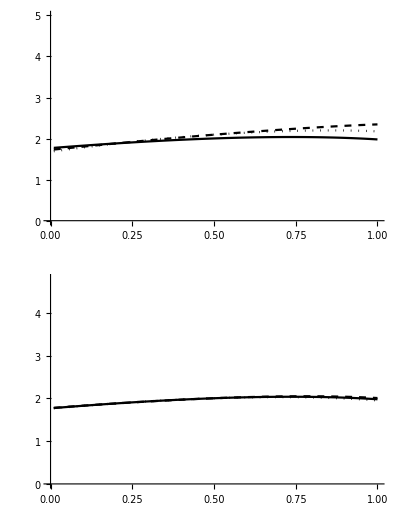
-Graphics-Sex-biased dispersal, d_m=1-d_fMale age at maturity, a_m

```mathematica
plotam=Labeled[GraphicsGrid[{{plotbattle1m},{plotbattle2m}}],{"Sex-biased dispersal, d_m=1-d_f","Male age at maturity, a_m"},{Bottom,Left},RotateLabel->True,LabelStyle->{FontFamily->"Helvetica"}]
```

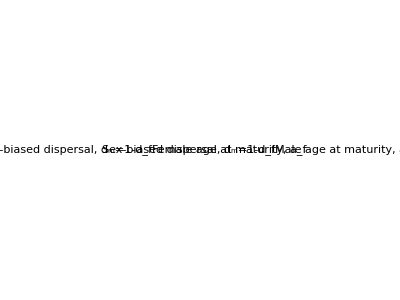

```mathematica
plotafam=GraphicsGrid[{{plotaf,plotam}}]
```

```mathematica
Export[$HomeDirectory<>"/Projects/age_vs_size_imprint/figs/effect_phil/battleground.pdf",plotafam]
```

/home/bram/Projects/age_vs_size_imprint/figs/effect_phil/battleground.pdf

## Results haplodiploidy

```mathematica
anshap[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdip/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
anshapM[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdipM/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
anshapP[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdipP/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
anshapMI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdipMI/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
anshapPI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdipPI/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ans[{4,4},{0.9,0.1,0.5},{1,1/3}]
```

{af→2.82018,am→2.84606}

### Figure S1

```mathematica
a1hap=Table[{{dm,af},{dm,am}}/.anshap[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a2hap=Table[{{dm,af},{dm,am}}/.anshapM[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a3hap=Table[{{dm,af},{dm,am}}/.anshapP[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a4hap=Table[{{dm,af},{dm,am}}/.anshapMI[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a5hap=Table[{{dm,af},{dm,am}}/.anshapPI[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
```

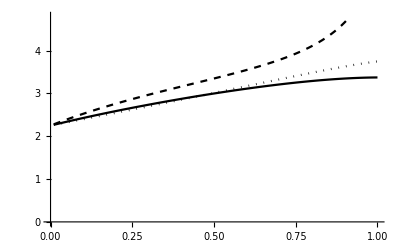

```mathematica
plotbattle1=ListLinePlot[{Transpose[a1hap][[1]],Transpose[a2hap][[1]],Transpose[a3hap][[1]]},PlotStyle->{{Black,Normal},{Black,Dashed},{Black,Dotted}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

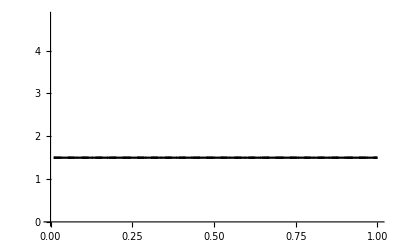

```mathematica
plotbattle1m=ListLinePlot[{Transpose[a1hap][[2]],Transpose[a2hap][[2]],Transpose[a3hap][[2]]},PlotStyle->{{Black,Normal},{Black,Dashed},{Black,Dotted}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

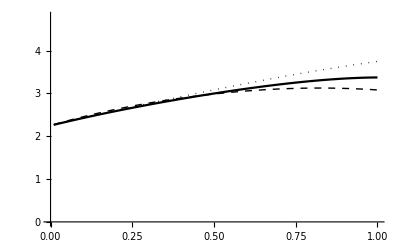

```mathematica
plotbattle2=ListLinePlot[{Transpose[a1hap][[1]],Transpose[a4hap][[1]],Transpose[a5hap][[1]]},PlotStyle->{{Black,Normal},{Black,Dashed,Thick},{Black,Dotted,Thick}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

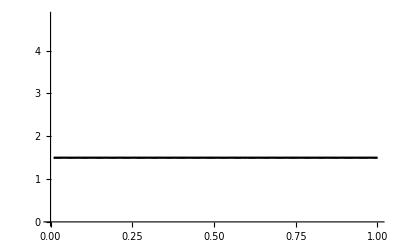

```mathematica
plotbattle2m=ListLinePlot[{Transpose[a1hap][[2]],Transpose[a4hap][[2]],Transpose[a5hap][[2]]},PlotStyle->{{Black,Normal},{Black,Dashed,Thick},{Black,Dotted,Thick}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

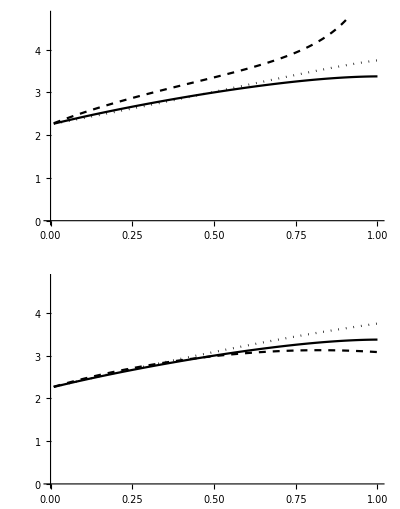
-Graphics-Sex-biased dispersal, d_m=1-d_fFemale age at maturity, a_f

```mathematica
plotaf=Labeled[GraphicsGrid[{{plotbattle1},{plotbattle2}}],{"Sex-biased dispersal, d_m=1-d_f","Female age at maturity, a_f"},{Bottom,Left},RotateLabel->True,LabelStyle->{FontFamily->"Helvetica"}]
```

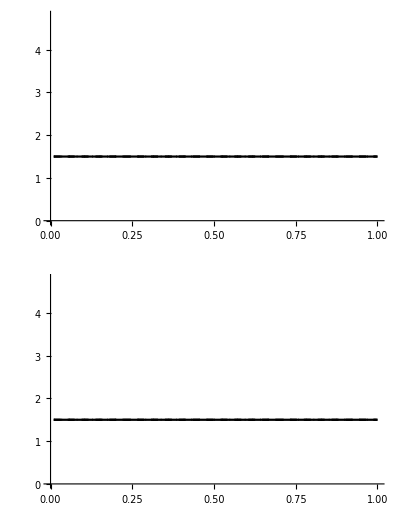
-Graphics-Sex-biased dispersal, d_m=1-d_fMale age at maturity, a_m

```mathematica
plotam=Labeled[GraphicsGrid[{{plotbattle1m},{plotbattle2m}}],{"Sex-biased dispersal, d_m=1-d_f","Male age at maturity, a_m"},{Bottom,Left},RotateLabel->True,LabelStyle->{FontFamily->"Helvetica"}]
```

```mathematica
plotafam=GraphicsGrid[{{plotaf,plotam}}]
```

-Graphics-

```mathematica
Export[$HomeDirectory<>"/Projects/age_vs_size_imprint/figs/effect_phil/battleground_haplodiploid.pdf",plotafam,ImageSize->{475,250}]
```

/home/bram/Projects/age_vs_size_imprint/figs/effect_phil/battleground_haplodiploid.pdf

## Export to R

```mathematica
rlistdip={{"dip",rdip},{"dipM",rdipM},{"dipP",rdipP},{"dipMI",rdipMI},{"dipPI",rdipPI}};
rlisthapdip={{"hapdip",rhapdip},{"hapdipM",rhapdipM},{"hapdipP",rhapdipP},{"hapdipMI",rhapdipMI},{"hapdipPI",rhapdipPI}};
```

```mathematica
str="";
For[iter=1,iter≤Length[rlistdip],iter++,
str=str<>"af"<>rlistdip[[iter,1]]<>"<-expression("<>ToString[CForm[selgradaf/.rlistdip[[iter,2]]/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}]]<>")\n\n";
str=str<>"am"<>rlistdip[[iter,1]]<>"<-expression("<>ToString[CForm[selgradam/.rlistdip[[iter,2]]/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}]]<>")\n\n";
]
For[iter=1,iter≤Length[rlisthapdip],iter++,
str=str<>"af"<>rlisthapdip[[iter,1]]<>"<-expression("<>ToString[CForm[selgradaf/.rlisthapdip[[iter,2]]/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}]]<>")\n\n";
str=str<>"am"<>rlisthapdip[[iter,1]]<>"<-expression("<>ToString[CForm[selgradam/.rlisthapdip[[iter,2]]/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}]]<>")\n\n";
]
```

```mathematica
Export[$HomeDirectory<>"/Projects/age_vs_size_imprint/figs/effect_phil/mathematica_expressions_r.txt",str]
```

/home/bram/Projects/age_vs_size_imprint/figs/effect_phil/mathematica_expressions_r.txt

```mathematica
e
```

e

## Export to Python

```mathematica
rlistdip={{"dip",rdip},{"dipM",rdipM},{"dipP",rdipP},{"dipMI",rdipMI},{"dipPI",rdipPI}};
rlisthapdip={{"hapdip",rhapdip},{"hapdipM",rhapdipM},{"hapdipP",rhapdipP},{"hapdipMI",rhapdipMI},{"hapdipPI",rhapdipPI}};
```

```mathematica
str="";
For[iter=1,iter≤Length[rlistdip],iter++,
str=str<>"af"<>rlistdip[[iter,1]]<>" = "<>ToString[CForm[selgradaf/.rlistdip[[iter,2]]/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}]]<>"\n\n";
str=str<>"am"<>rlistdip[[iter,1]]<>" = "<>ToString[CForm[selgradam/.rlistdip[[iter,2]]/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}]]<>"\n\n";
]
For[iter=1,iter≤Length[rlisthapdip],iter++,
str=str<>"af"<>rlisthapdip[[iter,1]]<>" = "<>ToString[CForm[selgradaf/.rlisthapdip[[iter,2]]/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}]]<>"\n\n";
str=str<>"am"<>rlisthapdip[[iter,1]]<>" = "<>ToString[CForm[selgradam/.rlisthapdip[[iter,2]]/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}]]<>"\n\n";
]
```

```mathematica
Export[$HomeDirectory<>"/Projects/age_vs_size_imprint/figs/effect_phil/mathematica_expressions_python.txt",str]
```

/home/bram/Projects/age_vs_size_imprint/figs/effect_phil/mathematica_expressions_python.txt

```mathematica
e
```

e